```mathematica
FourierTransform[Exp[-(ρ^2 + (v t - z)^2)/(2σ^2)]/(2 π σ^2)^(3/2),t,ω,FourierParameters->{1,1}]
```

(ⅇ^(1/2 (-ρ^2/σ^2+(ω (2 ⅈ v z-σ^2 ω))/v^2)))/(2 π √(v^2/σ^2) (σ^2)^(3/2))

```mathematica
ComplexPlot3D[ⅈ x/(ⅈ x - 1) Exp[ⅈ x/Sqrt[1-ⅈ x]-ⅈ x  -x^2],{x,-5-5ⅈ,+5+5ⅈ},PlotRange->{0,10}]
```

-Graphics3D-

```mathematica
z=0;
F[x_]:=ⅈ x/(ⅈ x - 1) Exp[ⅈ x/Sqrt[1-ⅈ x]-ⅈ x  -x^2]
```

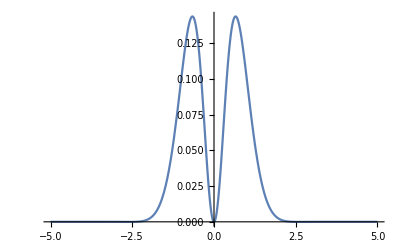

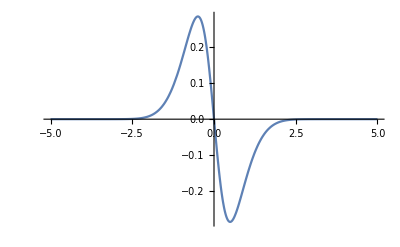

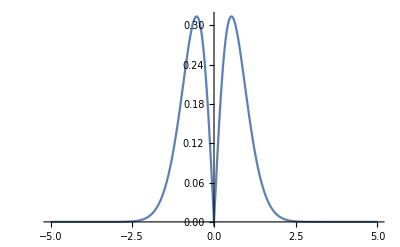

```mathematica
Plot[Re[F[x]],{x,-5,5},PlotRange->All]
Plot[Im[F[x]],{x,-5,5},PlotRange->All]
Plot[Abs[F[x]],{x,-5,5},PlotRange->All]
```

Why is there a nonzero Imaginary part?

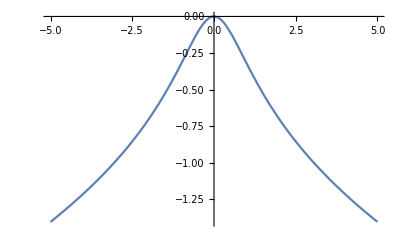

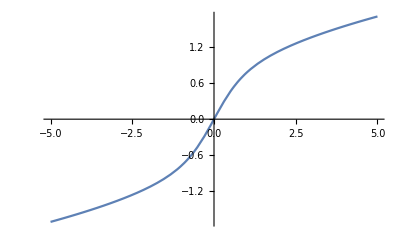

```mathematica
Plot[-x/(1+x^2)^(1/4)Sin[-1/2 Arg[1-ⅈ x]],{x,-5,5}]
Plot[x/(1+x^2)^(1/4)Cos[-1/2 Arg[1-ⅈ x]],{x,-5,5}]
```

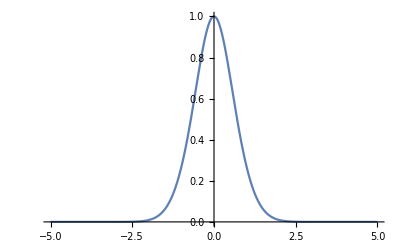

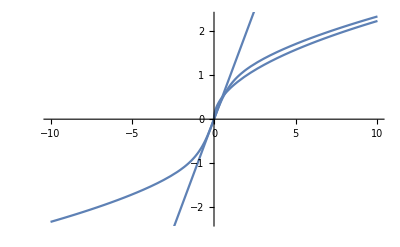

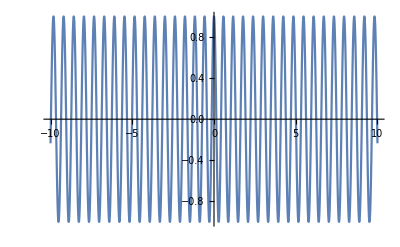

```mathematica
r = 1;
t=10;
ψ[ω_]:=ⅈ ω r/Sqrt[1-ⅈ ω];
Plot[Exp[Re[ψ[x]]-x^2 ],{x,-5,5},PlotRange->All]

A = Plot[Im[ψ[x]],{x,-10,10}];
B = Plot[Sqrt[x/2] r,{x,-10,10}];
CC = Plot[x r,{x,-10,10}];
Show[A,B,CC]
Plot[Cos[Im[ψ[x]]+x t] ,{x,-10,10}]
```

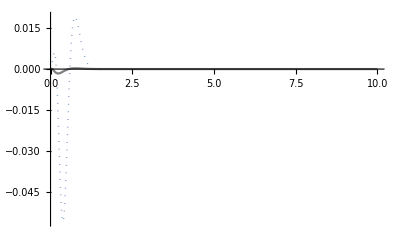

```mathematica
r=10;
t=1;
ψ[ω_]:=ⅈ ω r/Sqrt[1-ⅈ ω];
A=Plot[x^2/(1+x^2)Exp[Re[ψ[x]]-x^2]Cos[Im[ψ[x]]-x t],{x,0,10},PlotRange->All,PlotStyle->{Dotted,Thick}];
B=Plot[x^2/(1+x^2)Exp[-Sqrt[x/2] r-x^2]Cos[Sqrt[x/2]r -x t],{x,0,10},PlotRange->All,PlotStyle->Gray];
Show[A,B]
```